# Coherent states

## setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2024\Notebooks QKT

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## definitions

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,a2,Sy,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
(*Estados coherentes*)
Clear[a2];
a2[J_,Q_,P_]:=Module[{z=-1+(Q^2+P^2)/2,ϕ=ArcTan[-(P/Q)]},
N[Table[1/((1+Tan[ArcCos[-z]/2]^2)^J)Sqrt[Binomial[2J,J+(m-J)]] Tan[ArcCos[-z]/2]^(J+(m-J))Exp[-I(J+(m-J))ϕ],{m,0,2J}],20]
];

Clear[F];
F[J_,α_,k_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α)(Sz[J])]];

Clear[Tq];
Tq[q_]:=Module[{a,b,points=allpointsx[[q]]},
{a,b}=CoefficientList[Fit[points,{1,x},x],x];
{qlist[[q]],-b}
];

Clear[IPR];
IPR[J_,q_,ini_]:=Module[{a},
Log[Total[Abs[Conjugate[eigen].ini]^(2q)]]
];

Clear[Dq];
Dq[Q_,P_,q_,J_]:=Module[{floq=eigen,cohe=Quiet[a2[J,Q,P]],a},
a=(1/(1-q))Log[Total[Abs[Conjugate[floq].cohe]^(2q)]]/Log[2J+1]
];

Clear[H];
H[J_,α_,k_]:=N[(k/(2J))(Sx[J].Sx[J])+(α)(Sz[J])];

Clear[Qp,Q,P];
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
Q[J_]:=Qp[J]+Transpose[Qp[J]];
P[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
```

## Estados

```mathematica
Qs={{1/10,1},{15/10,1}};
```

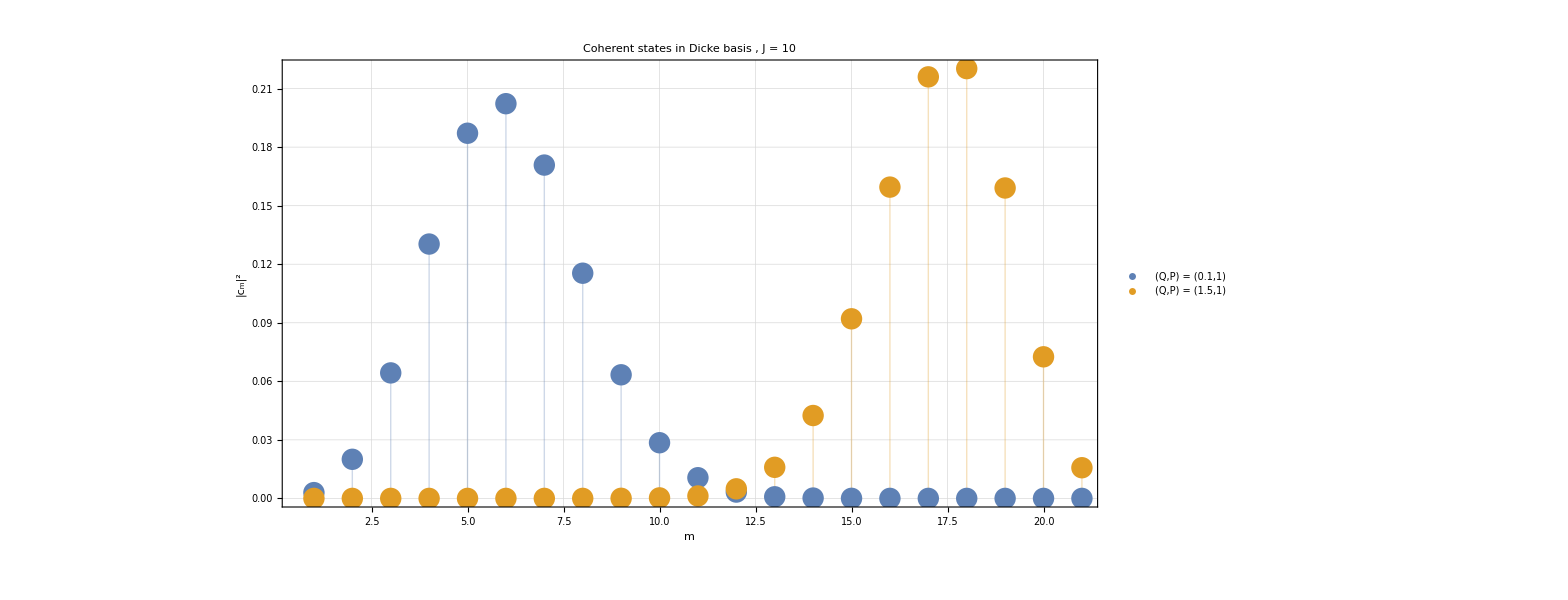

```mathematica
J=10;
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
ldos=ListPlot[Abs[cohes]^2,PlotRange->{All,All},PlotTheme->"Detailed",ImageSize->1200,Joined->False,FrameLabel->{"m","|c_m|^2"},PlotLabel->Row[{Style["Coherent states in Dicke basis , J = "<>ToString[J], 35,Black]}],LabelStyle->Directive[ 35,Black],AspectRatio->1/2,Filling->Axis,PlotLegends->{Style["(Q,P) = (0.1,1)",20,Black],Style["(Q,P) = (1.5,1)",20,Black]}]
```

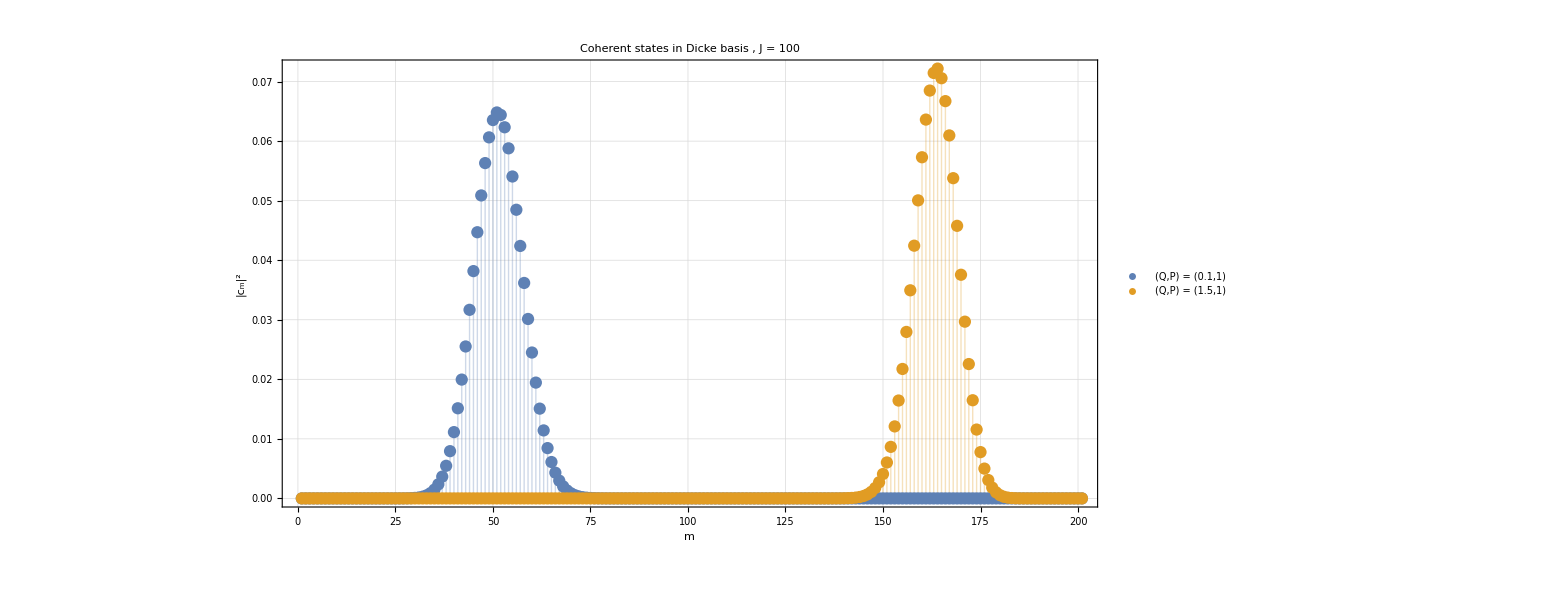

```mathematica
J=100;
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
ldos=ListPlot[Abs[cohes]^2,PlotRange->{All,All},PlotTheme->"Detailed",ImageSize->1200,Joined->False,FrameLabel->{"m","|c_m|^2"},PlotLabel->Row[{Style["Coherent states in Dicke basis , J = "<>ToString[J], 35,Black]}],LabelStyle->Directive[ 35,Black],AspectRatio->1/2,Filling->Axis,PlotLegends->{Style["(Q,P) = (0.1,1)",20,Black],Style["(Q,P) = (1.5,1)",20,Black]}]
```

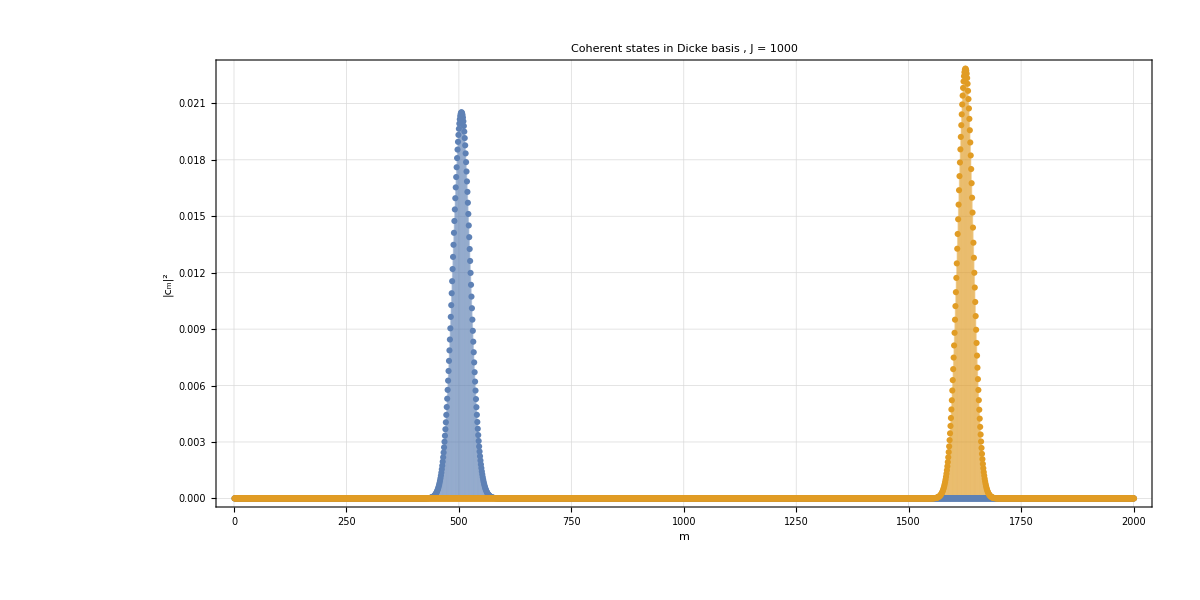

```mathematica
J=1000;
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
ldos=ListPlot[Abs[cohes]^2,PlotRange->{All,All},PlotTheme->"Detailed",ImageSize->1200,Joined->False,FrameLabel->{"m","|c_m|^2"},PlotLabel->Row[{Style["Coherent states in Dicke basis , J = "<>ToString[J], 35,Black]}],LabelStyle->Directive[ 35,Black],AspectRatio->1/2,Filling->Axis]
```

```mathematica
Qs={{1/10,1},{15/10,1}};
```

```mathematica
data1=ParallelTable[(Total[Abs[Quiet[a2[J,j[[1]],j[[2]]]]]^4]),{j,Qs},{J,1,1000,10}];
```

```mathematica
newdata1=Transpose[{Log[Range[1,1000,10]],Log[data1[[1]]]}];
newdata2=Transpose[{Log[Range[1,1000,10]],Log[data1[[2]]]}];
```

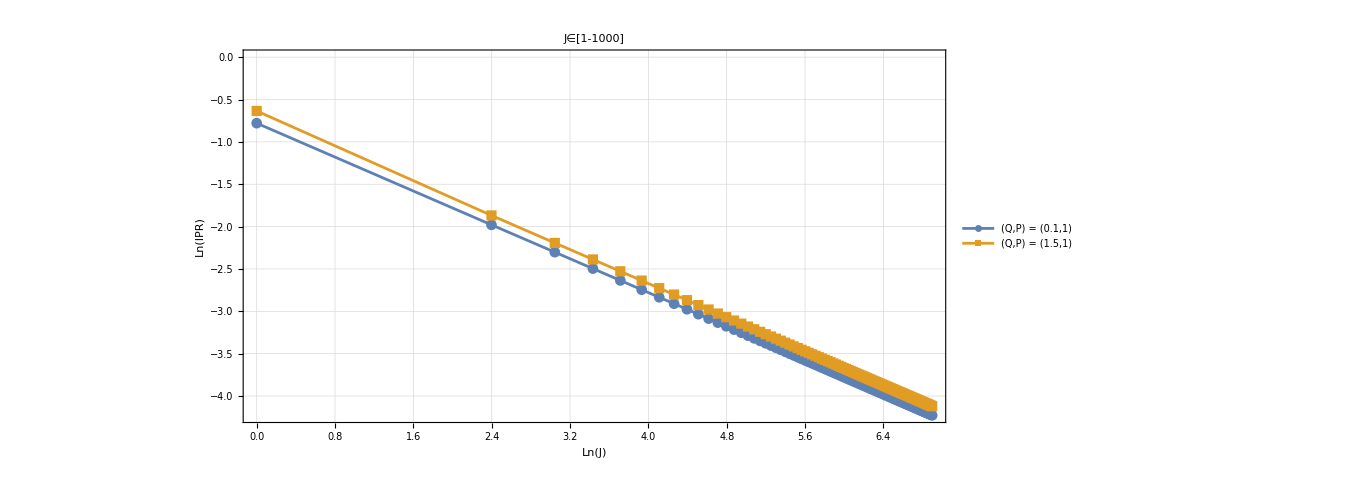

```mathematica
ListPlot[{newdata1,newdata2},PlotRange->All,PlotTheme->"Detailed",ImageSize->1000,PlotLabel->Style["J∈[1-1000]", 30,Black],FrameLabel->{Style["Ln(J)",25,Black],Style["Ln(IPR)",25,Black]},Joined->True,PlotMarkers->Automatic,LabelStyle->Directive[ 35,Black],AspectRatio->1/2,PlotLegends->{Style["(Q,P) = (0.1,1)",20,Black],Style["(Q,P) = (1.5,1)",20,Black]}]
```

## Husimis

```mathematica
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)],vec,alfa2},
vec=Table[If[alfa1==0&&i==-J,1,N[Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]]],{i,-J,J}];
Normalize[vec]
];
```

```mathematica
dq=0.020;
region=Flatten[ParallelTable[If[Sqrt[i^2+j^2]<2,{Rationalize[i],Rationalize[j]},{0,0}],{i,-2.0+dq,2.0-dq,dq},{j,-2.0+dq,2.0-dq,dq}],1];
region=DeleteCases[region,_{0,0}];
region=Sort[AppendTo[region,{0,0}]];
region//Dimensions
```

{31398,2}

```mathematica
puntos=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
data=ParallelTable[Abs[Conjugate[j].a2[J,i[[1]],i[[2]]]]^2,{i,Qs},{j,puntos}];
```

```mathematica
newdata1=Table[{region[[i,1]],region[[i,2]],data[[1]][[i]]},{i,Length[region]}];
newdata2=Table[{region[[i,1]],region[[i,2]],data[[2]][[i]]},{i,Length[region]}];
```

```mathematica
ListContourPlot[newdata1,PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",PlotTheme->"Detailed",ImageSize->600,InterpolationOrder->3,PlotLabel->Row[{Style["J = 100, (Q,P) = (0.1,1)", 30,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[newdata2,PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",PlotTheme->"Detailed",ImageSize->600,InterpolationOrder->3,PlotLabel->Row[{Style["J = 100, (Q,P) = (1.5,1)", 30,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[newdata1,PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",PlotTheme->"Detailed",ImageSize->600,InterpolationOrder->3,PlotLabel->Row[{Style["J = 10, (Q,P) = (0.1,1)", 30,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic]
```

-Graphics-

```mathematica
ListContourPlot[newdata2,PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",PlotTheme->"Detailed",ImageSize->600,InterpolationOrder->3,PlotLabel->Row[{Style["J = 10, (Q,P) = (1.5,1)", 30,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic]
```

-Graphics-